# AlgebraicRange

Generate ranges of algebraic numbers

## Definition

### Helper functions

#### FormulaComplexity

```mathematica
ClearAll[formulaComplexity,formulaComplexityHeuristic]

(*the built-in methods SimplifyCount and LeafCount have the disadvantage of not being continuous and thus of not allowing fine tuning of the output*)

digitSum[int_Integer]:=If[$VersionNumber>=14,DigitSum[int],Total@IntegerDigits[int]]

formulaComplexityHeuristic[form_?NumericQ]:=
	N@Total[Cases[
			Inactivate[form]
		/.const_?(Quiet@MemberQ[Attributes[#],Constant]&):>1
			/.c_Complex:>ReIm[c]
				/.r:Rational[i1_Integer,i2_Integer]:>{i1,i2}
					/.Inactive[Sqrt][arg_]:>Inactive[Sqrt[{arg,arg}]]
						/.Alternatives[
							Inactive[Power][b_,Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}],
							Inactive[Power][{b_},Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}]]:>
								Table[b,Abs[n]+Abs[m]],
			_Integer,{0,Infinity}]/. j_Integer?NonPositive:>-j+1
				/.i_Integer:>Mean[1/2{5IntegerLength[i],digitSum[i],Total[Last/@FactorInteger[i]],Sqrt[Abs[N[i]]]}]]

formulaComplexity[form_?NumericQ]:=
	formulaComplexityHeuristic[form]
```

#### Utilities

```mathematica
realReplace[x_]:=If[Head[x]===Real,RootApproximant[x],x]
```

```mathematica
cleanSort[list_List,wp_:MachinePrecision]:=SortBy[DeleteDuplicatesBy[list,N[#,wp]&],N[#,wp]&]
```

#### Error management

```mathematica
failureNotReal=
Failure["NotReal",<|"MessageTemplate"->"The input parameters `nr` are not real numbers.","MessageParameters"-><|"nr"->#|>|>]&;
failureNotAlg=Failure["NotAlgebraic",<|"MessageTemplate"->"The input parameters `na` are not algebraic numbers.","MessageParameters"-><|"na"->#|>|>]&;
failureFareyStep=Failure["FareyStep",<|"MessageTemplate"->"The step parameter `s` is not allowed with the Farey range option.","MessageParameters"-><|"s"->#|>|>]&;
failureLowerBound=
	Failure["LowerBound",<|"MessageTemplate"->"The steps' lower bound parameter `d` cannot be negative.","MessageParameters"-><|"d"->#|>|>]&;
failureUpperBound=
Failure["UpperLowerBound",<|"MessageTemplate"->"The steps' upper bound `s` cannot be lower than the lower bound `d` in absolute value.","MessageParameters"-><|"s"->#1,"d"->#2|>|>]&;
```

```mathematica
failureThrow[arg_]:=
	If[MemberQ[arg,_Failure|$Failed,{0,Infinity}],
		Throw@First@Union@Cases[arg,_Failure|$Failed,{0,Infinity}],
		arg]
```

### Basic range

#### Farey range

```mathematica
ClearAll[fareyRange]
fareyRange[r1_,r2_,r3_]:=
	Which[
		r3>=1,
			ResourceFunction["FareyRange"][r1,r2,r3],
		r3<=-1,
			Reverse[ResourceFunction["FareyRange"][r2,r1,-r3]],
		MatchQ[r3,Rational[1,_]],
			ResourceFunction["FareyRange"][r1,r2,1/r3],
		MatchQ[r3,Rational[-1,_]],
			Reverse[ResourceFunction["FareyRange"][r2,r1,-1/r3]],
		True,
			failureFareyStep[r3]]
```

#### Elementary range

```mathematica
ClearAll[elemRange]


(*1 argument*)

elemRange[{ord_},{r1_},opts:OptionsPattern[AlgebraicRange]]/;
r1>=1:=
	Range[1,r1^ord]^(1/ord)

elemRange[{ord_},{r1_},opts:OptionsPattern[AlgebraicRange]]/;
r1<1:=
	{}


(*2 arguments*)

elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;
0<=r1<=r2:=
	Range[r1^ord,r2^ord]^(1/ord)

elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;
r1<=r2<=0:=
	-Range[(-r1)^ord,(-r2)^ord,-1]^(1/ord)//Select[r1<=#<=r2&]

elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;
r1<0&&r2>=0:=
	Module[{elrg1,elrg2},
		elrg1=elemRange[{ord},{r1,0},opts];
		elrg2=elemRange[{ord},{0,r2},opts];
		If[IntegerQ[(-r1)^ord]&&IntegerQ[r2^ord]&&Length[elrg1]>0&&Length[elrg2]>0,
			elrg1~Join~Drop[elrg2,1],
			elrg1~Join~elrg2]]
(*drop the zero element to avoid duplication*)

elemRange[{ord_},{r1_,r2_},opts:OptionsPattern[AlgebraicRange]]/;
r2<r1:=
	{}


(*2 arg. step -1: reverse direction*)

elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;
r1>=r2>=0:=
	Range[r1^ord,r2^ord,-1]^(1/ord)

elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;
r2<=r1<=0:=
	-Range[(-r1)^ord,(-r2)^ord]^(1/ord)//Select[r2<=#<=r1&]

elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;
r2<0&&r1>=0:=
	Module[{elrg1,elrg2},
		elrg1=elemRange[{ord},{r1,0,-1},opts];
		elrg2=elemRange[{ord},{0,r2,-1},opts];
		If[IntegerQ[r1^ord]&&IntegerQ[(-r2)^ord]&&Length[elrg1]>0&&Length[elrg2]>0,
			elrg1~Join~Drop[elrg2,1],
			elrg1~Join~elrg2]]	

elemRange[{ord_},{r1_,r2_,-1},opts:OptionsPattern[AlgebraicRange]]/;
r2>r1:=
	{}


(*3 arguments, typically necessary with the option "StepMethod"->"Root"*)

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
0<=r1<=r2&&r3>0:=
	If[r3===1&&OptionValue["StepMethod"]=!="Root",
		elemRange[{ord},{r1,r2}],
		If[!OptionValue["FareyRange"],
			Range[r1^ord,r2^ord,r3^ord]^(1/ord),
			fareyRange[r1^ord,r2^ord,r3^ord]^(1/ord)]]
		
elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<=r2<=0&&r3>0:=
	If[r3===1&&OptionValue["StepMethod"]=!="Root",
		elemRange[{ord},{r1,r2}],
		If[!OptionValue["FareyRange"],
			-Range[(-r1)^ord,(-r2)^ord,-r3^ord]^(1/ord),
			-fareyRange[(-r1)^ord,(-r2)^ord,-r3^ord]^(1/ord)]//Select[r1<=#<=r2&]]

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<0&&r2>=0&&r3>0&&r3<=r2-r1:=
	Module[{elrg1,elrg2},
		elrg1=elemRange[{ord},{r1,0,r3},opts];
		elrg2=elemRange[{ord},{0,r2,r3},opts];
		If[Last[elrg1]===0&&Length[elrg1]>0&&Length[elrg2]>0,
			elrg1~Join~Drop[elrg2,1],
			elrg1~Join~elrg2]]

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<0&&r2>=0&&r3>0&&r3>r2-r1:=
	{r1}

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
0<=r2<=r1&&r3<0:=
	Range[r1^ord,r2^ord,-(-r3)^ord]^(1/ord)

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<=r1<=0&&r3<0:=
	-Range[(-r1)^ord,(-r2)^ord,(-r3)^ord]^(1/ord)//Select[r2<=#<=r1&]


elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<0&&r1>=0&&r3<0&&Abs[r3]<=r1-r2:=
	Module[{elrg1,elrg2},
		elrg1=elemRange[{ord},{r1,0,r3},opts];
		elrg2=elemRange[{ord},{0,r2,r3},opts];
		If[Last[elrg1]===0&&Length[elrg1]>0&&Length[elrg2]>0,
			elrg1~Join~Drop[elrg2,1],
			elrg1~Join~elrg2]]
		
elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<0&&r1>=0&&r3<0&&Abs[r3]>r1-r2:=
	{r1}

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<r1&&r3>=0:=
	{}

elemRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<r2&&r3<=0:=
	{}
```

#### Step range

```mathematica
ClearAll[factorRange]
factorRange[{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]:=
	Block[{as,one,max,zero,rg1,rg2,wp=OptionValue[WorkingPrecision]},
		
		as=Abs[r3];
		one=Max[1,as];

		max=Which[
				r3>0&&r1>0,
					one Abs[r2]/Min[Abs[r1],Abs[r2]],
				r3>0&&r1<=0,
					Max[Abs[r1],Abs[r2]],
				r3<0&&r2>0,
					one Abs[r1]/Min[Abs[r1],Abs[r2]],
				r3<0&&r2<=0,
					Max[Abs[r1],Abs[r2]]];

		zero=Which[
				r3>0&&r1>0,
					Quotient[ r1/Max[Abs[r1],Abs[r2]]/one,as]as,
				r3>0&&r1<=0,
					0,
				r3<0&&r2>0,
					 Quotient[r2/Max[Abs[r1],Abs[r2]]/one,as]as,
				r3<0&&r2<=0,
					0];
		
		{rg1,rg2}=If[!OptionValue["FareyRange"],

						{Range[zero,one,as],Range[one,max,as]},
				
						If[IntegerQ[as],
							as=1/as];
						{fareyRange[zero,one,as],fareyRange[one,max,as]}
							//failureThrow];

		rg1=If[And[
				Length[rg1]>0,Last[rg1]===one,
				Length[rg2]>0,First[rg2]===one],
				
				Drop[rg1,-1],
				
				rg1];

		rg1~Join~rg2]
```

```mathematica
ClearAll[outerRange]

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<=r2&&r3>0&&r3<=r2-r1:=
	Block[{elrg,fcrg,i,j,curr,first,last,rg,flo,fhi,wp=OptionValue[WorkingPrecision]},

	elrg=elemRange[{ord},{If[r1>0,Min[r1,r1/r3],Max[r1,r1/r3]],r2},opts];
	fcrg=factorRange[{r1,r2,r3},opts];

	rg=CreateDataStructure["DynamicArray"];
	
	For[i=1,i<=Length[elrg],i++,
		
		curr=elrg[[i]];
		
		If[curr===0,rg["Append",0];Continue[]];

		If[curr>0,
			flo=r1/curr;fhi=r2/curr,
			flo=r2/curr;fhi=r1/curr];

		first=First@Nearest[fcrg->"Index",flo];
		While[first<=Length[fcrg]&&fcrg[[first]]<flo,first++];

		last=Last@Nearest[fcrg->"Index",fhi];
		While[last>=1&&fcrg[[last]]>fhi,last--];

		For[j=first,j<=last,j++,
			
			rg["Append",curr*fcrg[[j]]]]];

	cleanSort[rg//Normal,wp]]

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<=r1&&r3<0&&Abs[r3]<=r1-r2:=
	Block[{elrg,fcrg,i,j,curr,first,last,rg,flo,fhi,wp=OptionValue[WorkingPrecision]},

	elrg=elemRange[{ord},{If[r1>0,Min[r1,-r1/r3],Max[r1,-r1/r3]],r2,-1},opts];
	fcrg=factorRange[{r1,r2,r3},opts];

	rg=CreateDataStructure["DynamicArray"];
	
	For[i=1,i<=Length[elrg],i++,
		
		curr=elrg[[i]];

		If[curr===0,rg["Append",0];Continue[]];

		If[curr>0,
			flo=r2/curr;fhi=r1/curr,
			flo=r1/curr;fhi=r2/curr];

		first=First@Nearest[fcrg->"Index",flo];
		While[first<=Length[fcrg]&&fcrg[[first]]<flo,first++];

		last=Last@Nearest[fcrg->"Index",fhi];
		While[last>=1&&fcrg[[last]]>fhi,last--];

		For[j=first,j<=last,j++,

			rg["Append",curr*fcrg[[j]]]]];

	Reverse@cleanSort[rg//Normal,wp]]

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<=r2&&r3>0&&r3>r2-r1:=
	{r1}

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<=r1&&r3<0&&Abs[r3]>r1-r2:=
	{r1}

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r2<r1&&r3>=0:=
	{}

outerRange[{ord_},{r1_,r2_,r3_},opts:OptionsPattern[AlgebraicRange]]/;
r1<=r2&&r3<=0:=
	{}
```

```mathematica
ClearAll[stepRange]
stepRange[{ord_},{r1_,r2_,r3_:1},opts:OptionsPattern[AlgebraicRange]]:=
	Which[
		OptionValue["StepMethod"]==="Outer",
			outerRange[{ord},{r1,r2,r3},opts],	
		OptionValue["StepMethod"]==="Root",
			elemRange[{ord},{r1,r2,r3},opts]]
```

#### Restricted range

```mathematica
ClearAll[complexitySelect]
complexitySelect[list_List,c_]:=
	Select[list,formulaComplexity[#]<=c&]
```

```mathematica
ClearAll[stepSelect]
stepSelect[list_List,d_]:=
	Block[{sel,eln,i},
		sel=CreateDataStructure["DynamicArray"];
		eln=list[[1]];
		sel["Append",eln];
	
		For[i=2,i<=Length[list],i++,

			If[Abs[list[[i]]-eln]>=d,

				eln=list[[i]];
				sel["Append",eln];

				Continue[]]];

		sel//Normal]~Quiet~N::meprec

stepSelect[{},d_,t_:0]:=
	{}
```

```mathematica
ClearAll[restrictRange]
restrictRange[main_,DirectedInfinity[1],0,wp_:MachinePrecision]:=
	main
restrictRange[main_,DirectedInfinity[1],d_?NumericQ,wp_:MachinePrecision]/;d>0:=
	stepSelect[main,d]
restrictRange[main_,compl_,0,wp_:MachinePrecision]:=
	complexitySelect[main,compl]
restrictRange[main_,compl_,d_?NumericQ,wp_:MachinePrecision]/;d>0:=
	stepSelect[complexitySelect[main,compl],d]
```

### Main definition

```mathematica
ClearAll[AlgebraicRange,iAlgebraicRange]

Options[AlgebraicRange]=
{"RootOrder"->2,"FareyRange"->False,WorkingPrecision->MachinePrecision,"FormulaComplexity"->Infinity,"StepMethod"->"Outer","AlgebraicsOnly"->True};

(*internal main function*)

iAlgebraicRange[{ord_?NumericQ},{r1_,r2_,r3_:1},d_:0,opts:OptionsPattern[AlgebraicRange]]/;
ord>=1&&NumericQ[r3]&&d>=0:=

	Block[{o,x,y,s,mainrange,fullrange},

	{o,x,y,s}=realReplace/@{ord,r1,r2,r3};

	If[!Element[{o,x,y,s},Reals],
		Failure["NotReal",
		failureNotReal[Select[{o,x,y,s},!Element[#,Reals]&]]]//failureThrow];

	If[!Element[{o,x,y,s},Algebraics]&&OptionValue["AlgebraicsOnly"],
		Failure["NotAlgebraic",
		failureNotAlg[Select[{o,x,y,s},!Element[#,Algebraics]&]]]//failureThrow];

	If[d>Abs[r3],
		failureUpperBound[r3,d]//failureThrow];

	If[OptionValue["FareyRange"]&&IntegerQ[s],
		s=1/s];

	mainrange=
		If[MemberQ[{1,-1},r3],
			elemRange[{o},{x,y,r3},opts],
			stepRange[{o},{x,y,s},opts]];

	fullrange=mainrange;
(*in the extended paclet version here combinations of the basic range are made*)

	restrictRange[
		fullrange,
		OptionValue["FormulaComplexity"],d,OptionValue[WorkingPrecision]]//failureThrow]//Catch

iAlgebraicRange[ordL_List,rL_List,d_:0,opts:OptionsPattern[AlgebraicRange]]/;(Length[ordL]>=2&&d>=0):=
	Block[{stepNegQ,join,sort},
	stepNegQ=Length[rL]==3&&rL[[3]]<0;
	join=Join@@Map[failureThrow@iAlgebraicRange[{#},rL,d,opts]&,ordL];
	sort=If[stepNegQ,Reverse[#],#]&@cleanSort[join,OptionValue[WorkingPrecision]];
	If[d!=0,stepSelect[sort,d],sort]]//Catch

iAlgebraicRange[ord_Integer,rL_List,d_:0,opts:OptionsPattern[AlgebraicRange]]/;d>=0:=
	iAlgebraicRange[Range[2,ord],rL,d,opts]

(*external main function*)

AlgebraicRange[r1_?NumericQ,r2_?NumericQ,r3_:1,d_:0,opts:OptionsPattern[AlgebraicRange]]/;
NumericQ[r3]&&d>=0:=
	iAlgebraicRange[OptionValue["RootOrder"],{r1,r2,r3},d,opts]

AlgebraicRange[r1_?NumericQ,opts:OptionsPattern[AlgebraicRange]]:=
	iAlgebraicRange[OptionValue["RootOrder"],{1,r1,1},0,opts]

AlgebraicRange[_,_,_,d_,opts:OptionsPattern[AlgebraicRange]]/;
d<0:=
	failureLowerBound[d]
```

## Documentation

### Usage

AlgebraicRange[x]

gives the range of square roots Sqrt[Range[1,x^2]], for x>=1.

AlgebraicRange[x,y]

gives the range of square roots Sqrt[Range[x^2,y^2]], for 0<=x<=y.

AlgebraicRange[x,y,s]

generates steps bounded above by s, with 0<s<=y.

AlgebraicRange[x,y,s,d]

requires the steps to be bounded below by d, with 0<=d<=s.

### Details & Options

AlgebraicRange creates ranges made of algebraic numbers. This extends the basic concept of Range to include, besides Rational numbers, also roots, always restricted to the Reals domain.

The first two arguments represent the bounds of the range (minimum and maximum values), while the optional third and fourth arguments (by default equal to 1 and 0) regulate the upper and lower bounds of the steps (differences between successive elements).

If no step parameter is specified, the elementary algebraic range AlgebraicRange[x,y] is determined by the square root range Sqrt[Range[x^2,y^2]], for x,y>0. The extension to negative bounds x <0 or y<0 is performed simply by reflection, since general real roots are mathematically defined only for positive arguments.

The step between successive algebraics is not straightforward to define univocally, as there exists no constant difference among the irrational numbers generated even with the elementary algebraic range. However, it turns out that an intuitively simple class of algebraic ranges, with non-unit step parameter s, is obtained by taking the Outer product of AlgebraicRange[Min[x,x/s],y] with Join[Range[0,Max[1, s], s], Range[Max[1, s], y, s]], for 0<s<=y-x and 0<=x<=y. Then the parameter s also becomes the upper bound for all the steps. For example, AlgebraicRange[0,2,1/2]={0,1/2,1/(√2),(√3)/2,1,√2,3/2,√3,2}.

This definition of algebraic step is more easily conveyed in terms of Outer, but if implemented literally it would lead to an intrinsically inefficient algorithm, for which Timing would scale quadratically with respect to the size of the input arguments. Thus, the actual algorithm implemented by AlgebraicRange generates output equivalent to Outer but is internally more refined - crucially leveraging the function Nearest inside For loops - and effectively scales with linear time complexity.

The algebraic numbers thus generated can often be in a great number, with a tendency to accumulate towards certain points. To avoid these features, a further fourth argument d can be optionally provided to require a minimum (absolute value) difference between successive algebraics, that is a lower bound for all the steps. This truncation process typically leads to a nearly uniform distribution of numeric values.

Extended functionality and syntax, especially for creating algebraic numbers of a more general form, are provided in the homonymous function of the paclet DanieleGregori/GeneralizedRange.

A natural application of AlgebraicRange is in the search for closed forms for floating point numbers, possibly in terms of arbitrary combinations of mathematical functions with algebraic arguments, through ResourceFunction["FindClosedForm"].

AlgebraicRange accepts the following options:

"RootOrder" | 2 | the root orders to be included
"StepMethod" | "Outer" | change the method to define the step
"FareyRange" | False | generate algebraic numbers with steps given by the Farey sequence
"FormulaComplexity" | Infinity | set a complexity threshold over which the algebraics are discarded
"AlgebraicsOnly" | True | accept only algebraic arguments and output
WorkingPrecision | MachinePrecision | set the precision for all internal numerical evaluations

The option "RootOrder" can take the following values:

r | include roots up to r order
{r} | include only roots of order r
{r_1,r_2,…} | include roots of all specified orders r_k

The option "StepMethod" can be used to define the step in AlgebraicRange[x,y,s] and can take the following values, for 0<=x<=y, 0<s<=y-x:

"Outer" | take the Outer product of AlgebraicRange[Min[x,x/s],y] with Join[Range[0,Max[1, s], s]],Range[Max[1, s], y, s]]
"Root" | use Sqrt[Range[x^2,y^2,s^2]]

A more detailed explanation of the step definition, also for negative arguments, can be found in the Properties and Relations examples.

Besides using the fourth argument to impose a lower bound on the steps, another way to restrict the output of AlgebraicRange is by setting a threshold for the complexity of the numeric expressions involved through the option "FormulaComplexity". The corresponding numerical values are not meaningful in practice and should be determined through a heuristic approach. A user interested in precise computations of the underlying homonymous function may use the paclet "DanieleGregori/GeneralizedRange".

## Examples

### Basic Examples

Generate a range of square roots:

```mathematica
range=AlgebraicRange[3]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3}

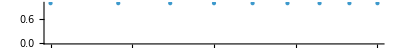

```mathematica
NumberLinePlot[range]
```

Generate a square root range with non-unit step:

```mathematica
range=AlgebraicRange[0,3,1/2]
```

{0,1/2,1/(√2),(√3)/2,1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

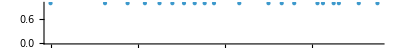

```mathematica
NumberLinePlot[range]
```

### Scope

Generate a range of negative square roots:

```mathematica
range=AlgebraicRange[-3,-1]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

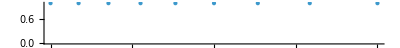

```mathematica
NumberLinePlot[range]
```

Generate a range of mixed positive and negative roots, with a negative step:

```mathematica
range=AlgebraicRange[2,-2,-1/2]
```

{2,√3,3/2,√2,1,(√3)/2,1/(√2),1/2,0,-1/2,-1/(√2),-(√3)/2,-1,-√2,-3/2,-√3,-2}

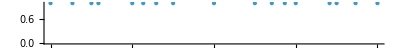

```mathematica
NumberLinePlot[range]
```

Generate a range of square roots, with certain upper and lower bounds on the steps:

```mathematica
range=AlgebraicRange[2,7,1/3,1/4]
```

{2,(√46)/3,2 √(5/3),(2 √19)/3,√10,2 √3,(5 √5)/3,4,(2 √41)/3,(2 √46)/3,√23,√26,√29,4 √2,√35,(7 √7)/3,5 √(5/3),3 √5,7}

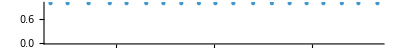

```mathematica
NumberLinePlot[range]
```

```mathematica
N@MinMax@Differences[range]
```

{0.252804,0.323944}

Generate a range of nested square roots:

```mathematica
AlgebraicRange[Sqrt[1+Sqrt[2]],7/2,1/Sqrt[2]]
```

{√(1+√2),√(1/2 (4+√2)),√(1/2 (5+√2)),√(2+√2),√(1/2 (6+√2)),√(1/2 (7+√2)),√(3+√2),√(1/2 (8+√2)),√(1/2 (9+√2)),√(4+√2),√(1/2 (10+√2)),√(5+√2),(1+1/(√2)) √(1+√2),√(6+√2),√(7+√2),√(8+√2),(1+1/(√2)) √(2+√2),√(9+√2),√(10+√2)}

### Options

#### RootOrder

Generate a range of square and cubic roots:

```mathematica
AlgebraicRange[2,"RootOrder"->3]
```

{1,2^(1/3),√2,3^(1/3),2^(2/3),5^(1/3),√3,6^(1/3),7^(1/3),2}

Generate a range of fourth roots:

```mathematica
AlgebraicRange[0,4,2,"RootOrder"->{4}]
```

{0,2,2 2^(1/4),2 3^(1/4),2 √2,2 5^(1/4),2 6^(1/4),2 7^(1/4),2 2^(3/4),2 √3,2 10^(1/4),2 11^(1/4),2 √2 3^(1/4),2 13^(1/4),2 14^(1/4),2 15^(1/4),4}

Generate a range of cube and fifth roots:

```mathematica
AlgebraicRange[1,3/2,"RootOrder"->{3,5}]
```

{1,2^(1/5),3^(1/5),2^(1/3),2^(2/5),5^(1/5),6^(1/5),3^(1/3),7^(1/5)}

Generate algebraic terms up to fourth root order and require a minimum absolute difference between successive roots:

```mathematica
AlgebraicRange[0,4,2,1/4,"RootOrder"->4]
```

{0,2,2 2^(1/4),2 3^(1/4),2 3^(1/3),2 2^(2/3),2 √3,2 14^(1/4)}

#### StepMethod

Change method to define the step:

```mathematica
rootRg=AlgebraicRange[0,3,1/3,"StepMethod"->"Root"]
```

{0,1/3,(√2)/3,1/(√3),2/3,(√5)/3,√(2/3),(√7)/3,(2 √2)/3,1,(√10)/3,(√11)/3,2/(√3),(√13)/3,(√14)/3,√(5/3),4/3,(√17)/3,√2,(√19)/3,(2 √5)/3,√(7/3),(√22)/3,(√23)/3,2 √(2/3),5/3,(√26)/3,√3,(2 √7)/3,(√29)/3,√(10/3),(√31)/3,(4 √2)/3,√(11/3),(√34)/3,(√35)/3,2,(√37)/3,(√38)/3,√(13/3),(2 √10)/3,(√41)/3,√(14/3),(√43)/3,(2 √11)/3,√5,(√46)/3,(√47)/3,4/(√3),7/3,(5 √2)/3,√(17/3),(2 √13)/3,(√53)/3,√6,(√55)/3,(2 √14)/3,√(19/3),(√58)/3,(√59)/3,2 √(5/3),(√61)/3,(√62)/3,√7,8/3,(√65)/3,√(22/3),(√67)/3,(2 √17)/3,√(23/3),(√70)/3,(√71)/3,2 √2,(√73)/3,(√74)/3,5/(√3),(2 √19)/3,(√77)/3,√(26/3),(√79)/3,(4 √5)/3,3}

Compare with the default "Outer" step method:

```mathematica
outerRg=AlgebraicRange[0,3,1/3]
```

{0,1/3,(√2)/3,1/(√3),2/3,(√5)/3,√(2/3),(√7)/3,(2 √2)/3,1,2/(√3),4/3,√2,(2 √5)/3,2 √(2/3),5/3,√3,(2 √7)/3,(4 √2)/3,2,√5,4/(√3),7/3,(5 √2)/3,√6,√7,8/3,2 √2,5/(√3),(4 √5)/3,3}

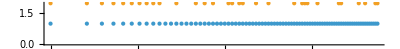

```mathematica
NumberLinePlot[{rootRg, outerRg},PlotLegends->{"Root","Outer"}]
```

#### FareyRange

Generate an algebraic range that generalizes ResourceFunction["FareyRange"]:

```mathematica
algFareyRg=AlgebraicRange[0,3,1/3,"FareyRange"->True]
```

{0,1/3,(√2)/3,1/2,1/(√3),2/3,1/(√2),(√5)/3,√(2/3),(√3)/2,(√7)/3,(2 √2)/3,1,(√5)/2,2/(√3),√(3/2),(√7)/2,4/3,√2,(2 √5)/3,3/2,2 √(2/3),5/3,√3,(2 √7)/3,(4 √2)/3,2,3/(√2),√5,4/(√3),7/3,(5 √2)/3,√6,5/2,(3 √3)/2,√7,8/3,2 √2,5/(√3),(4 √5)/3,3}

```mathematica
fareyRg=ResourceFunction["FareyRange"][0,3,3]
```

{0,1/3,1/2,2/3,1,4/3,3/2,5/3,2,7/3,5/2,8/3,3}

```mathematica
SubsetQ[algFareyRg,fareyRg]
```

True

Notice that the step parameter is originally the denominator of the step (both it and its reciprocal are accepted). This corresponds to the Union of ranges with steps equal to the elements of the FareySequence:

```mathematica
fareySq=FareySequence[3]~DeleteCases~0
```

{1/3,1/2,2/3,1}

```mathematica
SortBy[Union@Flatten@Map[AlgebraicRange[0,3,#]&,fareySq],N]==AlgebraicRange[0,3,3,"FareyRange"->True]
```

True

#### FormulaComplexity

With the default option "FormulaComplexity" set to Infinity, a very large number of algebraics can be produced:

```mathematica
AlgebraicRange[1,4,1,"RootOrder"->4]//Short
```

{1,2^(1/4),2^(1/3),3^(1/4),√2,3^(1/3),«304»,251^(1/4),√6 7^(1/4),253^(1/4),254^(1/4),255^(1/4),4}

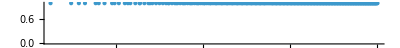

```mathematica
NumberLinePlot[%]
```

One way to limit these is by using the fourth argument, to require a minimum absolute difference between successive algebraics:

```mathematica
AlgebraicRange[1,4,1,1/10,"RootOrder"->4]
```

{1,2^(1/4),3^(1/4),3^(1/3),2^(2/3),5^(1/3),6^(1/3),15^(1/4),19^(1/4),23^(1/4),√2 7^(1/4),14^(1/3),2^(3/4) 5^(1/4),47^(1/4),55^(1/4),2 √2,74^(1/4),85^(1/4),97^(1/4),110^(1/4),5^(3/4),141^(1/4),159^(1/4),178^(1/4),199^(1/4),222^(1/4),246^(1/4)}

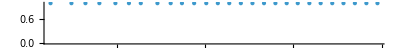

```mathematica
NumberLinePlot[%]
```

An alternative way is by setting the option "FormulaComplexity" to a finite threshold value, to select only numeric symbols with complexity less than that:

```mathematica
AlgebraicRange[4,"RootOrder"->4,"FormulaComplexity"->8]
```

{1,2^(1/4),2^(1/3),3^(1/4),√2,3^(1/3),2^(2/3),5^(1/3),√3,6^(1/3),7^(1/3),2,3^(2/3),√5,2 2^(1/4),√6,2 2^(1/3),2 3^(1/4),√7,2 √2,2 3^(1/3),3,√10,2 2^(2/3),√11,2 5^(1/3),2 √3,3 2^(1/4),√13,√14,3 2^(1/3),4}

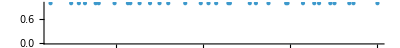

```mathematica
NumberLinePlot[%]
```

#### WorkingPrecision

If the step parameter is too small, some algebraic numbers may collide in their numerical values and get omitted in the output:

```mathematica
machPrecRg=With[{s=10^(-17)},
AlgebraicRange[Sqrt[1-25s],Sqrt[1+25s],s]]
```

{(√(3999999999999999/10))/20000000,(20000000000000001 √(3999999999999999/10))/400000000000000000000000,(12500000000000003 √(3999999999999999/10))/250000000000000000000000}

```mathematica
Min@Differences@N[machPrecRg,20]
```

5.×10^-17

To avoid this, increase the value of the option WorkingPrecision:

```mathematica
highPrecRg=With[{s=10^(-17)},
AlgebraicRange[Sqrt[1-25s],Sqrt[1+25s],s,WorkingPrecision->20]];
```

```mathematica
Short[highPrecRg,10]
```

{(√(3999999999999999/10))/20000000,(100000000000000001 √(3999999999999999/10))/2000000000000000000000000,(50000000000000001 √(3999999999999999/10))/1000000000000000000000000,(100000000000000003 √(3999999999999999/10))/2000000000000000000000000,«18»,(50000000000000011 √(3999999999999999/10))/1000000000000000000000000,(100000000000000023 √(3999999999999999/10))/2000000000000000000000000,(12500000000000003 √(3999999999999999/10))/250000000000000000000000,(4000000000000001 √(3999999999999999/10))/80000000000000000000000}

```mathematica
Min@Differences@N[highPrecRg,20]
```

1.×10^-17

Precision can be pushed arbitrarily high:

```mathematica
highPrecRg2=Block[{s=10^(-50),$MaxExtraPrecision=100},
AlgebraicRange[Sqrt[1-2s],Sqrt[1+2s],s,WorkingPrecision->60]]
```

{(√(49999999999999999999999999999999999999999999999999/2))/5000000000000000000000000,(100000000000000000000000000000000000000000000000001 √(49999999999999999999999999999999999999999999999999/2))/500000000000000000000000000000000000000000000000000000000000000000000000000,(50000000000000000000000000000000000000000000000001 √(49999999999999999999999999999999999999999999999999/2))/250000000000000000000000000000000000000000000000000000000000000000000000000}

```mathematica
N[highPrecRg2,60]//Column
```

0.99999999999999999999999999999999999999999999999999
1.
1.00000000000000000000000000000000000000000000000001

#### AlgebraicsOnly

By default, only algebraic numbers are accepted as input parameters:

```mathematica
AlgebraicRange[0,5,Sqrt[E]]
```

Failure[…]

Set this option to deliberately accept an output range which includes transcendental numbers:

```mathematica
AlgebraicRange[0,5,Sqrt[E],"AlgebraicsOnly"->False]
```

{0,√ⅇ,√(2 ⅇ),√(3 ⅇ),2 √ⅇ,√(5 ⅇ),√(6 ⅇ),√(7 ⅇ),2 √(2 ⅇ),3 √ⅇ}

```mathematica
Element[%,Algebraics]
```

False

### Applications

AlgebraicRange[x,y] is naturally suited for searching possible closed forms through ResourceFunction["FindClosedForm"]:

```mathematica
ResourceFunction["FindClosedForm"][1.05592,BarnesG,"SearchRange"->Function[AlgebraicRange[-#,#,"RootOrder"->4]]]
```

BarnesG[2^(1/4)]

```mathematica
N[%]
```

1.05592

Compare with the more complex result found with the "Plain" rational range:

```mathematica
ResourceFunction["FindClosedForm"][1.05592,BarnesG,"SearchRange"->"Plain"]
```

-1/63+BarnesG[4/3]

```mathematica
N[%]
```

1.05591

AlgebraicRange[x,y,s] provides a more general search range:

```mathematica
AlgebraicRange[-3,3,1/3,"RootOrder"->4]//Short
```

{-3,-2 5^(1/4),-(4 √5)/3,-79^(1/4),-78^(1/4),-(4 11^(1/3))/3,-(5 10^(1/4))/3,-26^(1/3),-77^(1/4),-√2 19^(1/4),«682»,77^(1/4),26^(1/3),(5 10^(1/4))/3,(4 11^(1/3))/3,78^(1/4),79^(1/4),(4 √5)/3,2 5^(1/4),3}

```mathematica
MemberQ[%,4/3]
```

True

The built-in function RootApproximant may have difficulty recognizing even relatively simple nested roots:

```mathematica
N[4 √(5+√2),10]
```

10.13051909

```mathematica
RootApproximant[%]//ToRadicals
```

1/17 (83+2 √1990)

In principle, these may be recognized by equipping ResourceFunction["FindClosedForm"] with a suitable search range in terms of AlgebraicRange[x,y,s]:

```mathematica
ResourceFunction["FindClosedForm"][10.13051909,Identity,"SearchRange"->Function[Join[AlgebraicRange[1,#,1/2],AlgebraicRange[Sqrt[1+Sqrt[2]],#,1/Sqrt[2]]]]]
```

4 √(5+√2)

### Properties and Relations

AlgebraicRange[x,y] always extends Range[x,y] if x, y are integers:

```mathematica
algrange=AlgebraicRange[2,5]
```

{2,√5,√6,√7,2 √2,3,√10,√11,2 √3,√13,√14,√15,4,√17,3 √2,√19,2 √5,√21,√22,√23,2 √6,5}

```mathematica
range=Range[2,5]
```

{2,3,4,5}

```mathematica
SubsetQ[algrange,range]
```

True

The extension may not be complete for rational or irrational arguments:

```mathematica
algrange=AlgebraicRange[3/Sqrt@2,4]
```

{3/(√2),√(11/2),√(13/2),√(15/2),√(17/2),√(19/2),√(21/2),√(23/2),5/(√2),3 √(3/2),√(29/2),√(31/2)}

```mathematica
range=Range[3/Sqrt@2,4]
```

{3/(√2),1+3/(√2)}

```mathematica
Complement[range,algrange]
```

{1+3/(√2)}

AlgebraicRange[x,y] for x<=y<0 is equivalent to Reverse[-AlgebraicRange[-y,-x]]:

```mathematica
AlgebraicRange[-3,-1]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

```mathematica
Reverse[-AlgebraicRange[1,3]]
```

{-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

Compute the algebraic range for 0<=x<=y and positive step upper bound s>0:

```mathematica
AlgebraicRange[1,3,1/2]
```

{1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

This is an equivalent calculation:

```mathematica
Select[SortBy[Outer[Times,Range[0,3,1/2],AlgebraicRange[1,3]]//Flatten//DeleteDuplicates,N],1<=#<=3&]
```

{1,(√5)/2,√(3/2),(√7)/2,√2,3/2,√3,2,3/(√2),√5,√6,5/2,(3 √3)/2,√7,2 √2,3}

An algebraic range with a negative irrational step size:

```mathematica
AlgebraicRange[3,3/2,-1/Sqrt[3]]
```

{3,2 √2,√3 (1+1/(√3)),√7,√6,√5,√2 (1+1/(√3)),2,√3,2 √(2/3),√(7/3)}

An equivalent calculation:

```mathematica
Select[ReverseSortBy[Outer[Times,Join[Range[0,1,1/Sqrt[3]],Range[1,3,1/Sqrt[3]]],Range[3^2,(3/2)^2,-1]^(1/2)]//Flatten//DeleteDuplicates,N],3/2<=#<=3&]
```

{3,2 √2,√3 (1+1/(√3)),√7,√6,√5,√2 (1+1/(√3)),2,√3,2 √(2/3),√(7/3)}

The starting point is always preserved:

```mathematica
AlgebraicRange[-3/2,3/2,1/3]
```

{-3/2,-(2 √5)/3,-(√5)/2,-1,-(√5)/3,-2/3,-1/2,-(√5)/6,-1/3,-1/6,0,1/3,(√2)/3,2/3,(2 √2)/3,1,4/3,√2}

```mathematica
AlgebraicRange[-Sqrt[2],3/2,1/3]
```

{-√2,-4/3,-1,-(2 √2)/3,-2/3,-(√2)/3,-1/3,0,1/3,(√2)/3,2/3,(2 √2)/3,1,4/3,√2}

```mathematica
AlgebraicRange[Sqrt[10],-Sqrt[10],-2]
```

{√10,√6,√2,0,-2,-2 √2}

```mathematica
AlgebraicRange[2Sqrt[2+Sqrt[3]],-2Sqrt[2+Sqrt[3]],-Sqrt[5]]//Simplify
```

{2 √(2+√3),√(3+4 √3),√(-2+4 √3),0,-√5,-√10}

The numbers generated always belong to the domains of Algebraics and Reals:

```mathematica
algrange=Block[{$MaxExtraPrecision=200000},AlgebraicRange[2Sqrt[1+Sqrt@RandomInteger[{2,5}]],-2Sqrt[1+Sqrt@RandomInteger[{2,5}]],-Sqrt[2]/RandomInteger[{2,5}],1/4,"RootOrder"->RandomInteger[{2,5},2]]]
```

{2 √(1+√5),2/3 √2 (-2+8 (1+√5)^(3/2))^(1/3),(-17+8 (1+√5)^(3/2))^(1/3),(-24+8 (1+√5)^(3/2))^(1/3),(-30+8 (1+√5)^(3/2))^(1/3),(-35+8 (1+√5)^(3/2))^(1/3),(1+√2) (-46+8 (1+√5)^(3/2))^(1/3),√(-10+4 (1+√5)),1/3 √2 (-17+8 (1+√5)^(3/2))^(1/3),1/3 √2 (-30+8 (1+√5)^(3/2))^(1/3),1/3 √2 (-39+8 (1+√5)^(3/2))^(1/3),1/3 √2 (-44+8 (1+√5)^(3/2))^(1/3),1/3 √2 (-46+8 (1+√5)^(3/2))^(1/3),0,-(√2)/3,-(2 2^(1/6))/3,-1,-1/3 √2 19^(1/3),-(√2 11^(1/3))/3^(2/3),-2/3 √2 7^(1/3),-3^(2/3),-2^(2/3) (1+(√2)/3),-(2 √2 7^(1/3))/3^(2/3),-4/3 2^(1/6) 7^(1/3),-(4 2^(1/6))/3^(1/3)}

```mathematica
Element[algrange,Algebraics]
```

True

```mathematica
Element[algrange,Reals]
```

True

### Possible Issues

Only real arguments are accepted:

```mathematica
AlgebraicRange[Sqrt[1-Sqrt[2]],4,1/Sqrt[2]]
```

Failure[…]

A simple numeric input can be automatically recognized with its exact expression:

```mathematica
range=AlgebraicRange[0.1,3.1]
```

{1/10,(√101)/10,(√201)/10,(√301)/10,(√401)/10,(√501)/10,(√601)/10,(√701)/10,(3 √89)/10,(√901)/10}

```mathematica
N[range]
```

{0.1,1.00499,1.41774,1.73494,2.0025,2.2383,2.45153,2.64764,2.83019,3.00167}

However, some numeric input is not adequately recognized:

```mathematica
approxrange=AlgebraicRange[1.266314886,3]
```

{,√(1+^2),√(2+^2),√(3+^2),√(4+^2),√(5+^2),√(6+^2),√(7+^2)}

```mathematica
N[approxrange]
```

{1.26631,1.61355,1.8983,2.14559,2.36718,2.56974,2.75745,2.93318}

In any case, the numeric difference with the corresponding exact expressions remains negligible:

```mathematica
range=AlgebraicRange[1/2Sqrt[5+Sqrt[2]],3]
```

{(√(5+√2))/2,√(1+1/4 (5+√2)),√(2+1/4 (5+√2)),√(3+1/4 (5+√2)),√(4+1/4 (5+√2)),√(5+1/4 (5+√2)),√(6+1/4 (5+√2)),√(7+1/4 (5+√2))}

```mathematica
N[range-approxrange]
```

{-2.53015×10^-10,-1.98566×10^-10,-1.68781×10^-10,-1.49328×10^-10,-1.35349×10^-10,-1.24681×10^-10,-1.16193×10^-10,-1.09232×10^-10}

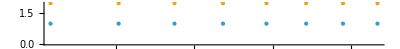

```mathematica
NumberLinePlot[{approxrange,range}]
```

Introducing a lower bound may cause the upper bound not to be respected anymore:

```mathematica
AlgebraicRange[-3,-1,1/3,1/4]
```

{-3,-8/3,-(5 √2)/3,-2,-√3,-√2,-2/(√3)}

```mathematica
Max@Differences@N[%]
```

0.357023

### Neat Examples

The implementation of AlgebraicRange[x,y,s] for step parameter s!=1 is more easily conveyed in terms of Outer as follows:

```mathematica
outerAlgebraicRange[x_,y_,s_]/;x<=y && 0<s<=y-x:=
Select[
SortBy[
Outer[
Times,
Join[
	Range[0,Max[1,s],s],
	Range[Max[1,s],Max[Abs[x],Abs[y]],s]],
AlgebraicRange[
	If[x>0,Min[x,x/s],Max[x,x/s]],
	y]]
		//Flatten,
	N],
x<=#<=y&]//
	DeleteDuplicatesBy[N]
```

```mathematica
outerRg=outerAlgebraicRange[0,2,2/3]
```

{0,2/3,(2 √2)/3,1,2/(√3),4/3,√2,5/3,√3,2}

```mathematica
AlgebraicRange[0,2,2/3]==outerRg
```

True

```mathematica
LeafCount[outerRg]
```

39

This apparently complicated definition has the advantage of typically leading to an output with shorter Length and which is less complex, say, in terms of LeafCount, than merely applying Sqrt to the Range of squared arguments:

```mathematica
rootAlgebraicRange[x_,y_,s_]/;0<=x<=y && s>0:=
	Sqrt[Range[x^2,y^2,s^2]]
```

```mathematica
rootRg=rootAlgebraicRange[0,2,2/3]
```

{0,2/3,(2 √2)/3,2/(√3),4/3,(2 √5)/3,2 √(2/3),(2 √7)/3,(4 √2)/3,2}

```mathematica
AlgebraicRange[0,2,2/3,"StepMethod"->"Root"]==rootRg
```

True

```mathematica
LeafCount[rootRg]
```

61

However, the above implementation in terms of Outer is also essentially inefficient, as it scales with quadratic time complexity with respect to the size of the input bounds or the length of the output range. The actual implementation of AlgebraicRange[x,y,s] is equivalent in terms of output result but it is also much more efficient, scaling with nearly linear time complexity.

Let us directly compare the performance of the outer and actual algorithms by an explicit computation, conveniently delegated to RemoteBatchSubmit:

```mathematica
maxs={10,30,60,100,150,200};
```

```mathematica
job=RemoteBatchSubmit[

CompoundExpression[

timesO={};timesA={};lens={};checks={};,

Table[

Block[{resO,resA,timeO,timeA,check,len},

{timeO,resO}=outerAlgebraicRange[0,r,1/2]//RepeatedTiming;
AppendTo[timesO,timeO];

{timeA,resA}=AlgebraicRange[0,r,1/2]//RepeatedTiming;
AppendTo[timesA,timeA];

check=resO==resA;
AppendTo[checks,check];

len=Length[resA];
AppendTo[lens,len];],

{r,maxs}],

<|"Bound"->maxs,"Match"->checks,"Length"->lens,"Time Outer"->timesO,"Time Actual"->timesA|>],

RemoteMachineClass->"Basic4x16"]
```

RemoteBatchJobObject[…]

After a few minutes (and a few credits spent) we get back the result:

```mathematica
job["JobStatus"]
```

Succeeded

```mathematica
job["EvaluationTiming"]
```

467.629

```mathematica
job["CreditsSpent"]
```

19.25 credits

```mathematica
results=job["EvaluationResult"]
```

<|Bound→{10,30,60,100,150,200},Match→{True,True,True,True,True,True},Length→{219,1956,7841,21774,48966,87044},Time Outer→{0.00608147,0.249424,2.58437,13.6658,50.8415,125.438},Time Actual→{0.00444521,0.0642533,0.385462,1.48681,4.48564,9.94056}|>

Also in Tabular form:

```mathematica
tabResults=Tabular[Transpose@Values[results],Keys[results]]
```

-Graphics-

Let us plot the resulting RepeatedTiming against the output Length, together with their quadratic and linear fits:

```mathematica
With[

{AC=ResourceFunction["AssociateColumns"]},

{lsLenTO=List@@@Normal@AC[tabResults,"Length"->"Time Outer"],
lsLenTA=List@@@Normal@AC[tabResults,"Length"->"Time Actual"]},

{quadfit=NonlinearModelFit[lsLenTO,a x^2+b x + c,{a,b,c},x]//Normal,
linfit=LinearModelFit[lsLenTA,x,x]//Normal,

colors={StandardBlue,StandardRed},pt=15,lsMax=Max[tabResults[All,"Length"]//Normal]},

Show[

ListPlot[
{lsLenTO,lsLenTA},
PlotStyle->Evaluate[Directive[#,PointSize[Large]]&/@colors],PlotRange->All],

Plot[{quadfit,linfit},{x,0,10^Ceiling[Log10[lsMax]]},PlotLegends->{Style["Outer\nalgorithm",pt],Style["Actual\nalgorithm",pt]},PlotStyle->colors],

AxesLabel->{Style["Length",pt],Style["Timing",pt]},ImageSize->Large]]
```

-Graphics-

## Source & Additional Information

### Contributed By

Daniele Gregori

### Keywords

range

algebraics

numbers

roots

combinations

closed form

search

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Range

PowerRange

AlgebraicNumber

AlgebraicIntegerQ

Algebraics

Root

### Related Resource Objects

FindClosedForm

TranscendentalRange

ComplexRange

FareyRange

PrimesBetween

DanieleGregori/GeneralizedRange

### Source/Reference Citation

Source, reference or citation information

### Links

Algebraic Number -- from Wolfram MathWorld

### Tests

#### Definitions

```mathematica
AR=AlgebraicRange;
```

```mathematica
testARbounds[x_,y_,ID_:"",ord_:2]:=
	Block[{input,expected,test},
		input=AR[x,y,"RootOrder"->ord];
		expected=
			Select[Which[
				0<=x<=y,Range[x^ord,y^ord]^(1/ord),
				x≤y≤0,-Range[x^ord,y^ord,-1]^(1/ord),
				x>y,{},
				x<0&&y>0,Module[{elrg1,elrg2},
								elrg1=-Range[(-x)^ord,0,-1]^(1/ord);
								elrg2=Range[0,y^ord]^(1/ord);
								If[IntegerQ[(-x)^ord]&&IntegerQ[y^ord]&&Length[elrg1]>0&&Length[elrg2]>0,
									Join[elrg1,Drop[elrg2,1]],
									Join[elrg1,elrg2]]]],x<=#<=y&];
		test=VerificationTest[
				input,expected,
				TestID->{
						ToString[gr],
						FromLetterNumber[PreIncrement@id],
						ID}~StringRiffle~"-"];
		Echo[input,"input"];
		test]
```

```mathematica
testARstep[x_,y_,s_,ID_:"",ord_:2]:=
	Block[{input,expected,test,diff},
		input=AR[x,y,s,"RootOrder"->ord];
		expected=
			Which[
				x<=y&&s>0&&If[x<0&&y>=0,s<=y-x,True],
				Select[SortBy[
				Outer[Times,
				Join[Range[0,Max[1,s],s],Range[Max[1,s],Max[Abs[x],Abs[y]],s]],
				AR[If[x>0,Min[x,x/s],Max[x,x/s]],y,"RootOrder"->ord]]
					//Flatten,N],
					x<=#<=y&]//DeleteDuplicatesBy[N],
				x>=y&&s<0&&If[y<0&&x>=0,-s<=x-y,True],
				Select[ReverseSortBy[
				Outer[Times,
				Join[Range[0,Max[1,-s],-s],Range[Max[1,-s],Max[Abs[x],Abs[y]],-s]],
				AR[If[x>0,Min[x,-x/s],Max[x,-x/s]],y,-1,"RootOrder"->ord]]
					//Flatten,N],
					y<=#<=x&]//DeleteDuplicatesBy[N],
				x<=y&&s<0,
				{},
				x>=y&&s>0,
				{},
				True,
				{x}];
		test=VerificationTest[
				input,expected,
				TestID->{
						ToString[gr],
						FromLetterNumber[PreIncrement@id],
						ID}~StringRiffle~"-"];
		Echo[input,"input"];
		diff=Differences[input];
		Echo[{N[#],#<=Abs[s]}&@Max[Abs/@diff],"steps u.b."];
		test]
```

#### Elementary range

```mathematica
gr=1;
```

```mathematica
id=0;
```

```mathematica
testARbounds[1,3,"2args_int_pos_pos"]
```

input  {1,√2,√3,2,√5,√6,√7,2 √2,3}

TestObject[…]

```mathematica
testARbounds[-3,-1,"2args_int_neg_neg"]
```

input  {-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

TestObject[…]

```mathematica
testARbounds[-3,2,"2args_int_neg_pos"]
```

input  {-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1,0,1,√2,√3,2}

TestObject[…]

```mathematica
testARbounds[1/3,3,"2args_rat_pos_pos"]
```

input  {1/3,(√10)/3,(√19)/3,(2 √7)/3,(√37)/3,(√46)/3,(√55)/3,8/3,(√73)/3}

TestObject[…]

```mathematica
testARbounds[-3/2,-1/2,"2args_rat_neg_neg"]
```

input  {-3/2,-(√5)/2,-1/2}

TestObject[…]

```mathematica
testARbounds[-3,1,"2args_rat_neg_pos"]
```

input  {-3,-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1,0,1}

TestObject[…]

```mathematica
testARbounds[-3/2,5/3,"2args_rat_neg_pos"]
```

input  {-3/2,-(√5)/2,-1/2,0,1,√2}

TestObject[…]

```mathematica
testARbounds[Sqrt@6,5,"2args_irr_pos_pos"]
```

input  {√6,√7,2 √2,3,√10,√11,2 √3,√13,√14,√15,4,√17,3 √2,√19,2 √5,√21,√22,√23,2 √6,5}

TestObject[…]

```mathematica
testARbounds[-Sqrt@8,-1,"2args_irr_neg_neg"]
```

input  {-2 √2,-√7,-√6,-√5,-2,-√3,-√2,-1}

TestObject[…]

```mathematica
testARbounds[-Sqrt@6/7,7/3,"2args_irr_neg_pos"]
```

input  {-(√6)/7,0,1,√2,√3,2,√5}

TestObject[…]

```mathematica
testARbounds[4,3,"2args_empty_pos_pos"]
```

input  {}

TestObject[…]

```mathematica
testARbounds[3/2,-4/3,"2args_empty_pos_neg"]
```

input  {}

TestObject[…]

```mathematica
testARbounds[-Sqrt[3/2],-4,"2args_empty_neg_neg"]
```

input  {}

TestObject[…]

```mathematica
testARbounds[-2,-2,"2args_single_int_neg"]
```

input  {-2}

TestObject[…]

```mathematica
testARbounds[-3/2,-3/2,"2args_single_rat_neg"]
```

input  {-3/2}

TestObject[…]

```mathematica
testARbounds[-Sqrt@3/2,-Sqrt@3/2,"2args_single_irr_neg"]
```

input  {-(√3)/2}

TestObject[…]

```mathematica
testARbounds[Sqrt@7/6,Sqrt@7/6,"2args_single_irr_pos"]
```

input  {(√7)/6}

TestObject[…]

#### Step range - x>=0, y>=0

```mathematica
gr=2;
```

```mathematica
id=0;
```

```mathematica
testARstep[0,3,2,"3args_int_pos_pos_int_pos"]
```

input  {0,2,2 √2}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[1,Sqrt@5,1/3,"3args_irr_pos_pos_rat_pos"]
```

input  {1,2/(√3),4/3,√2,(2 √5)/3,5/3,√3,(4 √2)/3,2,√5}

steps u.b.  {0.236068,True}

TestObject[…]

```mathematica
testARstep[1,Sqrt@5,1/Sqrt@3,"3args_irr_pos_pos_irr_pos"]
```

input  {1,2/(√3),√(5/3),√2,1+1/(√3),√3,2,1+2/(√3),√2 (1+1/(√3)),√5}

steps u.b.  {0.267949,True}

TestObject[…]

```mathematica
testARstep[Sqrt@2,Sqrt@8,2/Sqrt@3,"3args_irr_pos_pos_irr_pos_large"]
```

input  {√2,√(10/3),√(14/3),√6,√(22/3),2 √2}

steps u.b.  {0.411528,True}

TestObject[…]

```mathematica
testARstep[4,2,-1/3,"3args_int_pos_pos_rat_neg"]
```

input  {4,√15,(8 √2)/3,√14,(5 √5)/3,√13,(4 √7)/3,2 √3,10/3,√11,4 √(2/3),√10,3,(4 √5)/3,2 √2,8/3,√7,2 √(5/3),(2 √14)/3,√6,(2 √13)/3,4/(√3),√5,(2 √11)/3,(2 √10)/3,2}

steps u.b.  {0.162278,True}

TestObject[…]

```mathematica
testARstep[4,2,-4/3,"3args_int_pos_pos_rat_neg_large"]
```

input  {4,(8 √2)/3,(4 √7)/3,4 √(2/3),(4 √5)/3,8/3}

steps u.b.  {0.314757,True}

TestObject[…]

```mathematica
testARstep[4,2,-2,"3args_int_pos_pos_rat_neg_single"]
```

input  {4}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[2,4,-7/3,"3args_int_pos_pos_rat_neg_empty"]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

#### Step range - x<=0, y<=0

```mathematica
gr=3;
```

```mathematica
id=0;
```

```mathematica
testARstep[-4,-2,2/3,"3args_int_neg_neg_rat_pos"]
```

input  {-4,-√15,-√14,-(5 √5)/3,-√13,-2 √3,-10/3,-√11,-√10,-3,-2 √2,-8/3,-√7,-2 √(5/3),-(2 √14)/3,-√6,-(2 √13)/3,-4/(√3),-√5,-(2 √11)/3,-(2 √10)/3,-2}

steps u.b.  {0.171573,True}

TestObject[…]

```mathematica
testARstep[-3,-1/2,1/2,"3args_rat_neg_neg_rat_pos"]
```

input  {-3,-2 √2,-√7,-(3 √3)/2,-5/2,-√6,-√5,-3/(√2),-2,-√3,-3/2,-√2,-(√7)/2,-√(3/2),-(√5)/2,-1,-(√3)/2,-1/(√2),-1/2}

steps u.b.  {0.267949,True}

TestObject[…]

```mathematica
testARstep[-5/2,-1/2,1/2,"3args_rat_neg_neg_rat_pos_bis"]
```

input  {-5/2,-(√21)/2,-9/4,-√5,-(√17)/2,-(√13)/2,-(3 √5)/4,-3/2,-5/4,-(√21)/4,-(√5)/2,-(√17)/4,-1,-(√13)/4,-3/4,-(√5)/4,-1/2}

steps u.b.  {0.258777,True}

TestObject[…]

```mathematica
testARstep[-3,-1/2,1/Sqrt@2,"3args_rat_neg_neg_irr_pos"]
```

input  {-3,-√3 (1+1/(√2)),-2 √2,-√7,-√6,-√2 (1+1/(√2)),-√5,-3/(√2),-2,-√(7/2),-√3,-1-1/(√2),-√(5/2),-√2,-√(3/2),-1,-1/(√2)}

steps u.b.  {0.292893,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@3,-1/Sqrt@2,1/Sqrt@8,"3args_irr_neg_neg_irr_pos"]
```

input  {-√3,-1-1/(√2),-√2,-1-1/(2 √2),-√(3/2),-1,-1/(√2)}

steps u.b.  {0.292893,True}

TestObject[…]

```mathematica
testARstep[-2Sqrt@8,-Sqrt@2,4/Sqrt@3,"3args_irr_pos_pos_irr_pos_large"]
```

input  {-4 √2,-4 √(5/3),-8/(√3),-4,-4 √(2/3)}

steps u.b.  {0.734014,True}

TestObject[…]

```mathematica
testARstep[-2,-3,-1/4,"3args_int_neg_neg_rat_neg"]
```

input  {-2,-3/(√2),-√5,-9/4,-√6,-5/2,-√7,-(5 √5)/4,-2 √2,-3}

steps u.b.  {0.19949,True}

TestObject[…]

```mathematica
testARstep[-1/2,-2,-4/3,"3args_rat_neg_neg_rat_neg_large"]
```

input  {-1/2,-(√73)/6,-(√137)/6}

steps u.b.  {0.924001,True}

TestObject[…]

```mathematica
testARstep[-1/7,-7/2,-7/3,"3args_rat_neg_neg_rat_neg_large_bis"]
```

input  {-1/7,-(√2410)/21,-(√4811)/21}

steps u.b.  {2.19485,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@5,-2 Sqrt@5,-5,"3args_irr_pos_pos_int_neg_single"]
```

input  {-√5}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[-4,6,-2,"3args_int_pos_pos_rat_neg_empty"]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

#### Step range - x y <=0

```mathematica
gr=4;
```

```mathematica
id=0;
```

```mathematica
testARstep[-4,4,2,"3args_int_neg_pos_int_pos"]
```

input  {-4,-2 √3,-2 √2,-2,0,2,2 √2,2 √3,4}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[-4,4,3,"3args_int_neg_pos_int_pos_bis"]
```

input  {-4,-√7,0,3}

steps u.b.  {3.,True}

TestObject[…]

```mathematica
testARstep[-1,Sqrt@5,1/3,"3args_irr_neg_pos_rat_pos"]
```

input  {-1,-2/3,-1/3,0,1/3,(√2)/3,1/(√3),2/3,(√5)/3,(2 √2)/3,1,2/(√3),4/3,√2,(2 √5)/3,5/3,√3,(4 √2)/3,2,√5}

steps u.b.  {0.333333,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@5,Sqrt@5,1/Sqrt@3,"3args_irr_neg_pos_irr_pos"]
```

input  {-√5,-√2 (1+1/(√3)),-1-2/(√3),-2,-√3,-1-1/(√3),-√2,-√(5/3),-2/(√3),-1,-√(2/3),-1/(√3),0,1/(√3),√(2/3),1,2/(√3),√(5/3),√2,1+1/(√3),√3,2,1+2/(√3),√2 (1+1/(√3)),√5}

steps u.b.  {0.57735,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@2,Sqrt@8,2/Sqrt@3,"3args_irr_neg_pos_irr_pos_large"]
```

input  {-√2,-√(2/3),0,2/(√3),2 √(2/3),2,4/(√3),2 √(5/3),2 √2}

steps u.b.  {1.1547,True}

TestObject[…]

```mathematica
testARstep[-2,8,10,"3args_int_neg_pos_int_pos_large_bis"]
```

input  {-2,0}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[-2,8,10.1,"3args_int_neg_pos_rat_pos_large_single"]
```

input  {-2}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[-2,8,-1.1,"3args_int_neg_pos_rat_neg_empty"]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[4,-2,-1/3,"3args_int_pos_neg_rat_neg"]
```

input  {4,√15,(8 √2)/3,√14,(5 √5)/3,11/3,√13,(4 √7)/3,2 √3,10/3,√11,(7 √2)/3,4 √(2/3),√10,3,(4 √5)/3,5/(√3),2 √2,8/3,√7,2 √(5/3),(2 √14)/3,√6,(2 √13)/3,(5 √2)/3,7/3,4/(√3),√5,(2 √11)/3,(2 √10)/3,2,(4 √2)/3,(2 √7)/3,√3,5/3,2 √(2/3),(2 √5)/3,√2,4/3,√(5/3),(√14)/3,(√13)/3,2/(√3),(√11)/3,(√10)/3,1,(2 √2)/3,(√7)/3,√(2/3),(√5)/3,2/3,1/(√3),(√2)/3,1/3,0,-1/3,-(√2)/3,-1/(√3),-2/3,-(2 √2)/3,-1,-2/(√3),-4/3,-√2,-5/3,-√3,-(4 √2)/3,-2}

steps u.b.  {0.333333,True}

TestObject[…]

```mathematica
testARstep[2,-5,-4/3,"3args_int_pos_neg_rat_neg_large"]
```

input  {2,(2 √5)/3,4/3,2/3,0,-4/3,-(4 √2)/3,-4/(√3),-8/3,-(4 √5)/3,-4 √(2/3),-(4 √7)/3,-(8 √2)/3,-4,-(4 √10)/3,-(4 √11)/3,-8/(√3),-(4 √13)/3,-(4 √14)/3}

steps u.b.  {1.33333,True}

TestObject[…]

```mathematica
testARstep[2,-5,-7,"3args_int_pos_neg_rat_neg_large_bis"]
```

input  {2,0}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[4,-2,-6.01,"3args_int_pos_neg_rat_neg_single"]
```

input  {4}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[2,4,-7/3,"3args_int_pos_pos_rat_neg_empty"]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

#### Restricted range

```mathematica
gr=5;
```

```mathematica
id=0;
```

```mathematica
VerificationTest[
	AR[2,5,1/3,1/4]//EchoLabel["input"],
	{2,4/(√3),2 √(5/3),(2 √19)/3,√10,2 √3,(5 √5)/3,4,√19,8/(√3),2 √6},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_pos_pos_pos_pos_expl"}]]
```

input  {2,4/(√3),2 √(5/3),(2 √19)/3,√10,2 √3,(5 √5)/3,4,√19,8/(√3),2 √6}

TestObject[…]

```mathematica
VerificationTest[
	Max@Differences@AR[2,5,1/3,1/4]>=1/4,
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_pos_pos_pos_pos_diff"}]]
```

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,-1,1/2,1/3]//EchoLabel["input"],
	{-3,-√7,-√5,-√3,-(√7)/2},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_neg_neg_pos_pos_expl"}]]
```

input  {-3,-√7,-√5,-√3,-(√7)/2}

TestObject[…]

```mathematica
VerificationTest[
	Max@Differences@AR[-3,-1,1/2,1/3]>=1/3,
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_neg_neg_pos_pos_diff"}]]
```

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,3,2/3,2/5]//EchoLabel["input"],
	{-3,-√6,-2,-(2 √5)/3,-1,0,2/3,2/(√3),2 √(2/3),√5,√7},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_neg_pos_pos_pos_expl"}]]
```

input  {-3,-√6,-2,-(2 √5)/3,-1,0,2/3,2/(√3),2 √(2/3),√5,√7}

TestObject[…]

```mathematica
VerificationTest[
	Max@Differences@AR[-3,3,2/3,2/5]>=2/5,
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"4args_neg_pos_pos_pos_diff"}]]
```

TestObject[…]

#### RootOrder

```mathematica
gr=6;
```

```mathematica
id=0;
```

```mathematica
testARstep[-4,4,2,"ord3_int_neg_pos_int_pos",3]
```

input  {-4,-2 7^(1/3),-2 6^(1/3),-2 √3,-2 5^(1/3),-2 2^(2/3),-2 3^(1/3),-2 √2,-2 2^(1/3),-2,0,2,2 2^(1/3),2 √2,2 3^(1/3),2 2^(2/3),2 5^(1/3),2 √3,2 6^(1/3),2 7^(1/3),4}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[-3,3,2,"ord4_int_neg_pos_int_pos",4]
```

input  {-3,-65^(1/4),-19^(1/3),-√7,-33^(1/4),-√5,-11^(1/3),-17^(1/4),-3^(1/3),-1,0,2,2 2^(1/4),2 2^(1/3),2 3^(1/4),2 √2,2 3^(1/3),2 5^(1/4)}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[-4,4,3,"ord5_int_neg_pos_int_pos",5]
```

input  {-4,-781^(1/5),-√5 7^(1/4),-538^(1/5),-37^(1/3),-295^(1/5),-94^(1/4),-√7,-2^(2/5) 13^(1/5),-10^(1/3),-13^(1/4),0,3,3 2^(1/5),3 2^(1/4),3 3^(1/5),3 2^(1/3),3 3^(1/4),3 2^(2/5)}

steps u.b.  {3.,True}

TestObject[…]

```mathematica
testARstep[-1,Sqrt@5,1/3,"ord3_irr_neg_pos_rat_pos",3]
```

input  {-1,-2/3,-1/3,0,1/3,2^(1/3)/3,(√2)/3,1/3^(2/3),2^(2/3)/3,5^(1/3)/3,1/(√3),2^(1/3)/3^(2/3),7^(1/3)/3,2/3,1/3^(1/3),10^(1/3)/3,11^(1/3)/3,(√5)/3,(2 2^(1/3))/3,(2 √2)/3,2/3^(2/3),1,(2 2^(2/3))/3,(2 5^(1/3))/3,2/(√3),(2 2^(1/3))/3^(2/3),2^(1/3),(2 7^(1/3))/3,4/3,2/3^(1/3),√2,(2 10^(1/3))/3,3^(1/3),(2 11^(1/3))/3,(2 √5)/3,2^(2/3),5/3,(4 2^(1/3))/3,5^(1/3),√3,6^(1/3),(4 √2)/3,7^(1/3),4/3^(2/3),2,3^(2/3),(5 2^(1/3))/3,(4 2^(2/3))/3,10^(1/3),11^(1/3),√5}

steps u.b.  {0.333333,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@5,Sqrt@5,2/Sqrt@3,"ord3_irr_neg_pos_irr_pos",3]
```

input  {-√5,-(2 (-1+(15 √15)/8)^(1/3))/(√3),-(2 (-2+(15 √15)/8)^(1/3))/(√3),-√(11/3),-(2 (-3+(15 √15)/8)^(1/3))/(√3),-(2 (-4+(15 √15)/8)^(1/3))/(√3),-√(7/3),-(2 (-5+(15 √15)/8)^(1/3))/(√3),-(2 (-6+(15 √15)/8)^(1/3))/(√3),-1,-(2 (-7+(15 √15)/8)^(1/3))/(√3),0,2/(√3),(2 2^(1/3))/(√3),2 √(2/3),2/3^(1/6),(2 2^(2/3))/(√3),(2 5^(1/3))/(√3),2,(2 2^(1/3))/3^(1/6),(2 7^(1/3))/(√3)}

steps u.b.  {1.1547,True}

TestObject[…]

```mathematica
testARstep[-Sqrt@2,Sqrt@8,2/Sqrt@3,"ord4_irr_neg_pos_irr_pos_large",4]
```

input  {-√2,-√(2/3) 5^(1/4),-(2 (-1+(3 √(3/2))/2)^(1/3))/(√3),-√(2/3),0,2/(√3),(2 2^(1/4))/(√3),(2 2^(1/3))/(√3),2/3^(1/4),2 √(2/3),2/3^(1/6),(2 5^(1/4))/(√3),2 (2/3)^(1/4),(2 2^(2/3))/(√3),(2 7^(1/4))/(√3),(2 2^(3/4))/(√3),(2 5^(1/3))/(√3),2,(2 10^(1/4))/(√3),(2 2^(1/3))/3^(1/6),(2 11^(1/4))/(√3),(2 √2)/3^(1/4),(2 13^(1/4))/(√3),(2 7^(1/3))/(√3),(2 14^(1/4))/(√3),2 (5/3)^(1/4),4/(√3),(2 17^(1/4))/(√3),2 2^(1/4),2 3^(1/6),(2 19^(1/4))/(√3),2 √(2/3) 5^(1/4),2 (7/3)^(1/4),(2 10^(1/3))/(√3),(2 22^(1/4))/(√3),(2 23^(1/4))/(√3),(2 2^(3/4))/3^(1/4),(2 11^(1/3))/(√3),2 √(5/3),(2 26^(1/4))/(√3),2 3^(1/4),(2 2^(2/3))/3^(1/6),2 √(2/3) 7^(1/4),(2 29^(1/4))/(√3),2 (10/3)^(1/4),(2 13^(1/3))/(√3),(2 31^(1/4))/(√3),(4 2^(1/4))/(√3),2 (11/3)^(1/4),(2 14^(1/3))/(√3),(2 34^(1/4))/(√3),(2 35^(1/4))/(√3),2 √2}

steps u.b.  {1.1547,True}

TestObject[…]

```mathematica
testARstep[-2,8,10,"ord3_int_neg_pos_int_pos_large_bis",3]
```

input  {-2,0}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[-2,8,10.1,"ord3_int_neg_pos_rat_pos_large_single",3]
```

input  {-2}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[-2,8,-1.1,"ord3_int_neg_pos_rat_neg_empty",3]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[2,-1,-1/3,"ord3_int_pos_neg_rat_neg",3]
```

input  {2,4/3^(2/3),7^(1/3),(4 √2)/3,6^(1/3),√3,5^(1/3),(4 2^(1/3))/3,5/3,2^(2/3),3^(1/3),√2,4/3,(2 7^(1/3))/3,2^(1/3),(2 2^(1/3))/3^(2/3),2/(√3),(2 5^(1/3))/3,(2 2^(2/3))/3,1,2/3^(2/3),(2 √2)/3,(2 2^(1/3))/3,2/3,7^(1/3)/3,2^(1/3)/3^(2/3),1/(√3),5^(1/3)/3,2^(2/3)/3,1/3^(2/3),(√2)/3,2^(1/3)/3,1/3,0,-1/3,-2/3,-1}

steps u.b.  {0.333333,True}

TestObject[…]

```mathematica
testARstep[2,-1,-2/3,"ord4_int_pos_neg_rat_neg",4]
```

input  {2,(5 2^(1/4))/3,15^(1/4),14^(1/4),7^(1/3),13^(1/4),√2 3^(1/4),11^(1/4),6^(1/3),10^(1/4),√3,5^(1/3),2^(3/4),5/3,7^(1/4),2^(2/3),6^(1/4),5^(1/4),3^(1/3),√2,4/3,3^(1/4),(2 5^(1/4))/3^(3/4),(2 14^(1/4))/3,(2 7^(1/3))/3,(2 13^(1/4))/3,2^(1/3),(2 √2)/3^(3/4),(2 11^(1/4))/3,(2 2^(1/3))/3^(2/3),2^(1/4),(2 10^(1/4))/3,2/(√3),(2 5^(1/3))/3,(2 2^(3/4))/3,(2 7^(1/4))/3,(2 2^(2/3))/3,(2 2^(1/4))/3^(3/4),1,(2 5^(1/4))/3,2/3^(2/3),(2 √2)/3,2/3^(3/4),(2 2^(1/3))/3,(2 2^(1/4))/3,2/3,0,-2/3,-1}

steps u.b.  {0.666667,True}

TestObject[…]

```mathematica
testARstep[2,-3,-4/3,"ord3_int_pos_neg_rat_neg_large",3]
```

input  {2,4/3^(2/3),(2 19^(1/3))/3,(2 √5)/3,(2 11^(1/3))/3,4/3,2/3^(2/3),2/3,0,-4/3,-(4 2^(1/3))/3,-(4 √2)/3,-4/3^(2/3),-(4 2^(2/3))/3,-(4 5^(1/3))/3,-4/(√3),-(4 2^(1/3))/3^(2/3),-(4 7^(1/3))/3,-8/3,-4/3^(1/3),-(4 10^(1/3))/3,-(4 11^(1/3))/3,-(4 √5)/3}

steps u.b.  {1.33333,True}

TestObject[…]

```mathematica
testARstep[2,-5,-7,"ord3_int_pos_neg_rat_neg_large_bis",3]
```

input  {2,0}

steps u.b.  {2.,True}

TestObject[…]

```mathematica
testARstep[4,-2,-6.01,"ord3_int_pos_neg_rat_neg_single",3]
```

input  {4}

steps u.b.  {-∞,True}

TestObject[…]

```mathematica
testARstep[2,4,-7/3,"ord3_int_pos_pos_rat_neg_empty",3]
```

input  {}

steps u.b.  {-∞,True}

TestObject[…]

#### StepMethod

```mathematica
gr=7;
```

```mathematica
id=0;
```

```mathematica
VerificationTest[
	AR[2,3,1/2,"StepMethod"->"Root"]//EchoLabel["input"],
	Sqrt[Range[2^2,3^2,(1/2)^2]],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"stmet_pos_pos_pos"}]]
```

input  {2,(√17)/2,3/(√2),(√19)/2,√5,(√21)/2,√(11/2),(√23)/2,√6,5/2,√(13/2),(3 √3)/2,√7,(√29)/2,√(15/2),(√31)/2,2 √2,(√33)/2,√(17/2),(√35)/2,3}

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,-1,1/2,"StepMethod"->"Root"]//EchoLabel["input"],
	-Sqrt[Range[3^2,1^2,-(1/2)^2]],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"stmet_neg_neg_pos"}]]
```

input  {-3,-(√35)/2,-√(17/2),-(√33)/2,-2 √2,-(√31)/2,-√(15/2),-(√29)/2,-√7,-(3 √3)/2,-√(13/2),-5/2,-√6,-(√23)/2,-√(11/2),-(√21)/2,-√5,-(√19)/2,-3/(√2),-(√17)/2,-2,-(√15)/2,-√(7/2),-(√13)/2,-√3,-(√11)/2,-√(5/2),-3/2,-√2,-(√7)/2,-√(3/2),-(√5)/2,-1}

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,3,2/3,"StepMethod"->"Root"]//EchoLabel["input"],
	Join[-Sqrt[Range[3^2,0,-(2/3)^2]],Sqrt[Range[0,3^2,(2/3)^2]]]//DeleteDuplicates,
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"stmet_neg_pos_pos"}]]
```

input  {-3,-(√77)/3,-(√73)/3,-√(23/3),-(√65)/3,-(√61)/3,-√(19/3),-(√53)/3,-7/3,-√5,-(√41)/3,-(√37)/3,-√(11/3),-(√29)/3,-5/3,-√(7/3),-(√17)/3,-(√13)/3,-1,-(√5)/3,-1/3,0,2/3,(2 √2)/3,2/(√3),4/3,(2 √5)/3,2 √(2/3),(2 √7)/3,(4 √2)/3,2,(2 √10)/3,(2 √11)/3,4/(√3),(2 √13)/3,(2 √14)/3,2 √(5/3),8/3,(2 √17)/3,2 √2,(2 √19)/3,(4 √5)/3}

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,3,-2/3,"StepMethod"->"Root"]//EchoLabel["input"],
	{},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"stmet_neg_pos_neg"}]]
```

input  {}

TestObject[…]

#### FareyRange

```mathematica
gr=8;
```

```mathematica
id=0;
```

```mathematica
VerificationTest[
	AR[0,3,1/3,"FareyRange"->True]//EchoLabel["input"],
	SortBy[Union@Flatten@Map[AR[0,3,#]&,FareySequence[3]~DeleteCases~0],N],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"farey_pos_pos_pos"}]]
```

input  {0,1/3,(√2)/3,1/2,1/(√3),2/3,1/(√2),(√5)/3,√(2/3),(√3)/2,(√7)/3,(2 √2)/3,1,(√5)/2,2/(√3),√(3/2),(√7)/2,4/3,√2,(2 √5)/3,3/2,2 √(2/3),5/3,√3,(2 √7)/3,(4 √2)/3,2,3/(√2),√5,4/(√3),7/3,(5 √2)/3,√6,5/2,(3 √3)/2,√7,8/3,2 √2,5/(√3),(4 √5)/3,3}

TestObject[…]

```mathematica
VerificationTest[
	AR[-3,0,3,"FareyRange"->True]//EchoLabel["input"],
	SortBy[Union@Flatten@Map[AlgebraicRange[-3,0,#]&,FareySequence[3]~DeleteCases~0],N],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"farey_neg_neg_pos"}]]
```

input  {-3,-(4 √5)/3,-5/(√3),-2 √2,-8/3,-√7,-(3 √3)/2,-5/2,-√6,-(5 √2)/3,-7/3,-4/(√3),-√5,-3/(√2),-2,-(4 √2)/3,-(2 √7)/3,-√3,-5/3,-2 √(2/3),-3/2,-(2 √5)/3,-√2,-4/3,-(√7)/2,-√(3/2),-2/(√3),-(√5)/2,-1,-(2 √2)/3,-(√7)/3,-(√3)/2,-√(2/3),-(√5)/3,-1/(√2),-2/3,-1/(√3),-1/2,-(√2)/3,-1/3,0}

TestObject[…]

```mathematica
VerificationTest[
	AR[-2,2,4,"FareyRange"->True]//EchoLabel["input"],
	SortBy[Union@Flatten@Map[AlgebraicRange[-2,2,#]&,FareySequence[4]~DeleteCases~0],N],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"farey_neg_pos_pos"}]]
```

input  {-2,-(4 √2)/3,-5/(2 √2),-7/4,-√3,-5/3,-3/2,-√2,-4/3,-(3 √3)/4,-5/4,-2/(√3),-3/(2 √2),-1,-(2 √2)/3,-(√3)/2,-3/4,-1/(√2),-2/3,-1/(√3),-1/2,-(√2)/3,-(√3)/4,-1/(2 √2),-1/3,-1/4,0,1/4,1/3,1/(2 √2),(√3)/4,(√2)/3,1/2,1/(√3),2/3,1/(√2),3/4,(√3)/2,(2 √2)/3,1,3/(2 √2),2/(√3),5/4,(3 √3)/4,4/3,√2,3/2,5/3,√3,7/4,5/(2 √2),(4 √2)/3,2}

TestObject[…]

#### WorkingPrecision

```mathematica
gr=9;
```

```mathematica
id=0;
```

```mathematica
VerificationTest[
	With[{s=10^(-17)},
	AR[Sqrt[1-25s],Sqrt[1+25s],s]]//EchoLabel["input"],
	{(√(3999999999999999/10))/20000000,(20000000000000001 √(3999999999999999/10))/400000000000000000000000,(12500000000000003 √(3999999999999999/10))/250000000000000000000000},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"wp_pos_pos_pos_mp"}]]
```

input  {(√(3999999999999999/10))/20000000,(20000000000000001 √(3999999999999999/10))/400000000000000000000000,(12500000000000003 √(3999999999999999/10))/250000000000000000000000}

TestObject[…]

```mathematica
VerificationTest[
	With[{s=10^(-17)},
	AR[Sqrt[1-4s],Sqrt[1+4s],s,WorkingPrecision->30]]//EchoLabel["input"],
	{(√(24999999999999999/10))/50000000,(100000000000000001 √(24999999999999999/10))/5000000000000000000000000,(50000000000000001 √(24999999999999999/10))/2500000000000000000000000,(100000000000000003 √(24999999999999999/10))/5000000000000000000000000,(25000000000000001 √(24999999999999999/10))/1250000000000000000000000},
	TestID->StringRiffle[{ToString[gr],FromLetterNumber@PreIncrement[id],"wp_pos_pos_pos_30"}]]
```

input  {(√(24999999999999999/10))/50000000,(100000000000000001 √(24999999999999999/10))/5000000000000000000000000,(50000000000000001 √(24999999999999999/10))/2500000000000000000000000,(100000000000000003 √(24999999999999999/10))/5000000000000000000000000,(25000000000000001 √(24999999999999999/10))/1250000000000000000000000}

TestObject[…]

#### Benchmark

```mathematica
Needs["Benchmarking`"]
```

```mathematica
benchmarkMachine=Benchmark[]//First
```

{MachineName→macbookpro,System→Mac OS X x86 (64-bit),BenchmarkName→WolframMark,FullVersionNumber→14.3.0,Date→April 6, 2026,BenchmarkResult→3.406,TotalTime→4.064,Results→{{Data Fitting,0.244},{Digits of Pi,0.15},{Discrete Fourier Transform,0.508},{Eigenvalues of a Matrix,0.259},{Elementary Functions,0.501},{Gamma Function,0.357},{Large Integer Multiplication,0.283},{Matrix Arithmetic,0.074},{Matrix Multiplication,0.13},{Matrix Transpose,0.436},{Numerical Integration,0.442},{Polynomial Expansion,0.062},{Random Number Sort,0.238},{Singular Value Decomposition,0.189},{Solving a Linear System,0.191}}}

```mathematica
bmRefTime=benchmarkMachine~Lookup~"TotalTime"
```

4.064

```mathematica
idRefMachine="5115-76242-31166";
```

```mathematica
gr=10;
```

```mathematica
bench[1]:=First@RepeatedTiming[AR[200];]/bmRefTime
```

```mathematica
benchRef[1]=If[$MachineID==idRefMachine,
				bench[1],
				0.05890341845140033]
```

0.0556128

```mathematica
With[{id=1},
VerificationTest[
	bench[id]<2 benchRef[id],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber[id],"bench_pos"},"-"]]]
```

TestObject[…]

```mathematica
bench[2]:=First@RepeatedTiming[AR[200,-200,-1];]/bmRefTime
```

```mathematica
benchRef[2]=If[$MachineID==idRefMachine,
				bench[2],
				0.13278136340072577]
```

0.231839

```mathematica
With[{id=2},
VerificationTest[
	bench[id]<2 benchRef[id],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber[id],"bench_pos_neg"},"-"]]]
```

TestObject[…]

```mathematica
bench[3]:=First@RepeatedTiming[AR[-100,100,1/2];]/bmRefTime
```

```mathematica
benchRef[3]=If[$MachineID==idRefMachine,
				bench[3],
				1.8878414744459522]
```

2.11292

```mathematica
With[{id=3},
VerificationTest[
	bench[id]<2 benchRef[id],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber[id],"bench_neg_pos_pos"},"-"]]]
```

TestObject[…]

```mathematica
bench[4]:=First@RepeatedTiming[AR[60,-60,-1/3];]/bmRefTime
```

```mathematica
benchRef[4]=If[$MachineID==idRefMachine,
				bench[4],
				0.6905768882858436]
```

0.77684

```mathematica
With[{id=4},
VerificationTest[
	bench[id]<2 benchRef[id],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber[id],"bench_pos_neg_neg"},"-"]]]
```

TestObject[…]

```mathematica
bench[5]:=First@RepeatedTiming[Length@AR[1-10^(-13),1+10^(-13),10^(-17),WorkingPrecision->30];]/bmRefTime
```

```mathematica
benchRef[5]=If[$MachineID==idRefMachine,
				bench[5],
				0.05513387607417459]
```

0.0665949

```mathematica
With[{id=5},
VerificationTest[
	bench[id]<2 benchRef[id],
	TestID->StringRiffle[{ToString[gr],FromLetterNumber[id],"bench_pos_pos_pos_p30"},"-"]]]
```

TestObject[…]

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Extended functionality is provided in the homonymous function of the paclet "DanieleGregori/GeneralizedRange".

### Change Log

#### Version 2.0.0

More natural definition for negative bounds and non-unit step parameters, in some cases not backward compatible.

Improved algorithm for non-unit step parameter (under the default option "StepMethod" -> "Outer"), now scaling with linear time complexity.

Implementation of the new option WorkingPrecision, allowing generation of arbitrarily fine ranges.

Various other code and efficiency improvements.

Verified comprehensive tests and benchmarks.

## Submission Notes

Additional information for the reviewer.